# Pregunta 3

Para resolver la ecuacion x^3=±√(1-x^2) podemos elevar al cuadrado y tenemos x^6=1-x^2->x^6+x^2-1=0. Hacemos un cambio de variable y=x^2->y^3+y-1=0 y esta ecuación se puede resolver con el algoritmo de cardano. A partir de la solución y real de esta ecuación cúbica después obtenemos las 2 intersecciones x^2=y->x=±√y.

```mathematica
CubeSol=Cases[cardano[-1.,1,0,1],_Real][[1]](*Extraemos la solucion real*)
```

0.682328

```mathematica
(*Utilizamos la funcion cardano (internamente utiliza quadraticSolve) para extraer las dos raices*)
solutions=cardano[-CubeSol,0.,1,0.]
```

cardano::quadraticEq: this is a quadratic equation

{0.826031,-0.826031}

```mathematica
plot1=Plot[{x^3,√(1-x^2),-√(1-x^2)},{x,-1,1},AspectRatio->1,PlotRange->{{-1,1},{-1,1}},PlotLegends->"Expressions",PlotStyle->{Automatic,Orange,Orange},AxesLabel->{Style["x",15],Style["y",15]}];
```

```mathematica
line1=Graphics[{Dashed,Line[{{solutions[[1]],0},{solutions[[1]],solutions[[1]]^3}}]}];
line12=Graphics[{Dashed,Line[{{0,solutions[[1]]^3},{solutions[[1]],solutions[[1]]^3}}]}];
text1=Graphics[Text[solutions[[1]],{solutions[[1]],-0.07}]];
line2=Graphics[{Dashed,Line[{{solutions[[2]],0},{solutions[[2]],solutions[[2]]^3}}]}];
line22=Graphics[{Dashed,Line[{{0,solutions[[2]]^3},{solutions[[2]],solutions[[2]]^3}}]}];
text2=Graphics[Text[solutions[[2]],{solutions[[2]],0.07}]];
```

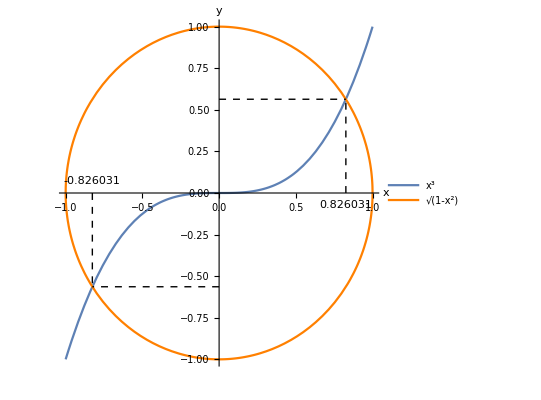

```mathematica
Show[plot1,line1,line12,line2,line22,text1,text2]
```